## K^* 介子

#### 求出共振态贡献。

{20.077,Null}

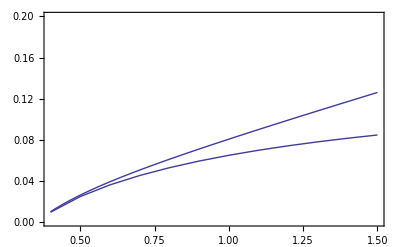

```mathematica
Clear[a, pts, plotres, plotsub, plotfull, f1, cont, contsubtract]
Λ=0.1; s0=1.7; up=13;
min =0.4; max=1.5;
a[M2_]:=(4π)/9 1/Log[M2/Λ^2]
f1[M2_]:=M2/(4π)(1+a[M2]/π-0.15 (0.6/M2)^2-0.14(0.6/M2)^3)
cont[M2_]:=∫_s0^up 1/(4π)(1+a[s]/π)E^(-s/M2)ⅆs//N
contsubtract[M2_]:=f1[M2]-cont[M2]
Timing[
pts = Table[contsubtract[M2],{M2,min,max, 0.1}] ;
]

dataKstar = Transpose[Join[{Range[min, max, 0.1]}, {pts}]];
plotsub=ListLinePlot[dataKstar];
plotfull=Plot[f1[M2],{M2,min, max}];
Show[{plotsub, plotfull}, PlotRange->{{min,max},{0.,0.2}},
AxesOrigin->{0.2,0.3}, Frame->True, Axes->False]
```

#### 确定合适的M^2的范围。

首先高阶修正小于总贡献的30%。

```mathematica
FindRoot[Abs[(-0.15 (0.6/M2)^2-0.14(0.6/M2)^3)/(1+a[M2]/π-0.15 (0.6/M2)^2-0.14(0.6/M2)^3)]==0.3,{M2,1}]
```

{M2→0.631476}

其次连续谱贡献小于总贡献的30%。

```mathematica
Timing[
Table[cont[M2]/(1+a[M2]/π-0.15 (0.6/M2)^2-0.14(0.6/M2)^3),{M2, 1., 2.0, 0.1}]
]
```

{18.424,{0.0155158,0.0196224,0.0240894,0.0288734,0.0339354,0.0392411,0.0447597,0.0504639,0.0563291,0.0623329,0.0684553}}

#### 拟合质量的平方和耦合常数的平方。

```mathematica
min =0.7; max=1.3; 
Timing[
pts = Table[contsubtract[M2],{M2,min,max, 0.1}] ;
]
dataKstar1 = Transpose[Join[{Range[min, max, 0.1]}, {pts}]];
FindFit[dataKstar1,(π m2)/g2 E^(-m2/M2), {g2,m2}, M2]
```

{11.622,Null}

{4.77396×10^-15,{g2→17.5475,m2→0.82112}}

```mathematica
4 π/0.72//N
```

17.4533

```mathematica
0.892^2
```

0.795664